# Presentations

Slide Show

Traditional Form for results

## Let’s begin:

```mathematica
data1 = Table[a^2, {a, 1, 10}]
```

```mathematica
{1,4,9,16,25,36,49,64,81,100}
```

Plot the Data

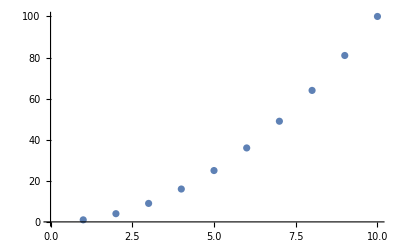

```mathematica
lpdata1 = ListPlot[data1]
```

Fit the Data

```mathematica
fitdata1 = Fit[data1,{1,x},x]
```

-22.+11. x

Plot the fit

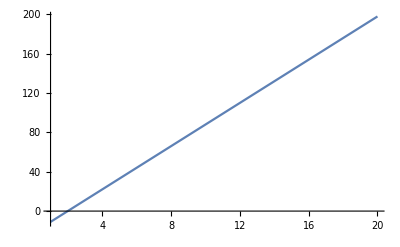

```mathematica
plotfitdata1 = Plot[fitdata1,{x,1,20}]
```

Combine the Graphics

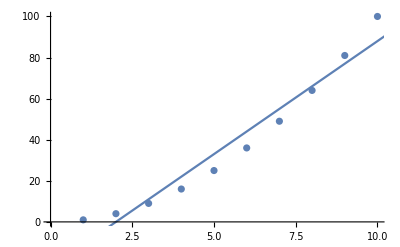

```mathematica
Show[lpdata1,plotfitdata1]
```